```mathematica
Get["C:\\Users\\diogo\\Dropbox\\Projeto PETRO\\Aquivos Mathematica\\diversos\\FORM.m"]
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[vars_,ov_,ec_,rs_]:=Block[{Po,siga,sigy,pi,d,t,young,nu,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

{siga,sigy,pi,d,t,young,nu}=vars;

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

initialguess=pi+deltaptresca;

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

(*Print["deltapy = ",deltapy];*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
H=Hfunc[ov,ec,rs];
(*H=0.22;*)
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKT[siga_,sigy_,pi_,d_,t_,young_,nu_,ov_,ec_,rs_]:=Block[{Po,feff,i,initialguess,min,tabguess,MisesEq,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},

deltaptresca=ky 2 sigy t/(d-t);

Ai=Pi/4 (d-2t)^2;
Ao=Pi/4 d^2;
As=Ao-Ai;
feff=siga As -pi Ai+po Ao;
(*feff=siga As ;*)
MisesEq=Sqrt[Abs[(ky(4./√3.)sigy t/(d-t))^2 (1.-(feff/(ky sigy As))^2)]]-po+pi;

(*initialguess=pi+deltaptresca;*)

tabguess=Table[{i,MisesEq/.po->i},{i,-30000,30000,1000}];
min=Min[Transpose[Abs[tabguess]][[2]]];
initialguess=0.;
For[i=1,i≤Length[tabguess],i++,If[Abs[tabguess[[i,2]]]==min,initialguess=tabguess[[i,1]]]];

Po=FindRoot[MisesEq,{po,initialguess},MaxIterations->100][[1,2]];

deltapmises=Po-pi;

If[deltapmises>deltaptresca,deltapy=(deltapmises+deltaptresca)/2,deltapy=deltapmises];

deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=Hfunc[ov,ec,rs];
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
(*Print["ColapseStrength = ",ColapseStrength];*)
ColapseStrength

]
```

```mathematica
ComputeNumericalGradKT[Vars_,Xvec_]:=Block[{vars,guess,dx=0.0001,xvecn,xvecn1,dgdx,derivative,i,X1,X2,X3,X4,X5,X6,X7,X8,X9,NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu},

{NofD,nYieldStrength,PintofD,PextofD,nDe,nt,nYoung,nNu}=Vars;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:=xvec[[1]]*ComputeColapseStrengthKT[NofD*xvec[[7]],nYieldStrength*xvec[[2]],PintofD*xvec[[8]],nDe,nt*xvec[[3]],nYoung,nNu,xvec[[4]],xvec[[5]],xvec[[6]]]-(PextofD*xvec[[9]]-PintofD*xvec[[8]]);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];
For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}(*/.{NofD->Vars[[1]],nYieldStrength->Vars[[2]],PintofD->Vars[[3]],PextofD->Vars[[4]],nDe->Vars[[5]],nt->Vars[[6]],nYoung->Vars[[7]],nNu->Vars[[8]]}*)
]
```

```mathematica
ComputeBurstResistance[n_,de_,t_,fu_,sa_,po_]:=Block[{a,kdr,kr,puts,pref,Futs,pfactor,pfactorNeck,pM,pBurstKS,pburst},
kdr=0.5^(n+1)+(1/√3)^(n+1);
kr=(4^(1-n)-1)*3^(n-1);
puts=(2 kdr t fu)/(de- t);
pref=(0.5^n*puts)/2(((2/√3)^(n+1))+1);
Futs=Pi t  fu(de-t);
pfactor=Sqrt[1-kr*(sa/fu)^2];
If[Abs[sa]<fu,a=(1-sa^2/fu^2)/(-3^(1-n)+4^(1-n)),a=0];
pfactorNeck=Sqrt[a];
pM=pref pfactor;
pBurstKS=po+Min[pM,(pM+0.5^n puts)/2];
If[sa/fu≤ ((√3)/2)^(1-n),
If[pM≤ (pM+0.5^n puts)/2,
pburst=po+pM;
,
pburst= po+(pM+0.5^n puts)/2;
],
pburst=po+pref*pfactorNeck;
];
pburst//N
];
```

```mathematica
ComputeNumericalGradKS[Vars_,Xvec_]:=Block[{n,de,t,fu,sa,pi,po,i,derivative,xvecn1,dgdx,dx=0.001,xvecn,NofD,x7,nYieldStrength,x3,PintofD,x8,nDe,nt,x2,nYoung,nNu,x4,x5,x6,x1,PextofD,x9,gx,grad,subst},
{n,de,t,fu,sa,pi,po}=Vars;
xvecn=Xvec;

(*KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}*)

Gx[xvec_]:= xvec[[1]]*ComputeBurstResistance[n,de,xvec[[3]]*t,xvec[[2]]*fu,xvec[[4]]*sa,xvec[[5]]*po]-(xvec[[6]] pi-xvec[[5]]*po);

derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

# -Graphics-

```mathematica
checkconv[vars_,pt_,GxGradx_]:=Block[{nsz=10,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate},
diffnorm=Table[0,{nsz}];
referenceresidual=GxGradx[vars,pt][[1]];
tan=GxGradx[vars,pt][[2]] ;
numrows=Length[pt];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range=pt/197;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];
Print["tan = ",tan];
Print["incval = ",incval];
estimateresidual=tan .incval;
Print["estimateresidual = ",estimateresidual];
For[i=1,i<nsz,i++,
actualstate=pt;
For[k=1,k≤numrows,k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
res=GxGradx[vars,actualstate][[1]];
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

72.7598

57.2133

15.5465

5000-po+9481.26 √(1.-8.84348×10^-13 (24863.3+72.7598 po)^2)

MisesEq[5000,po,9.625,0.545,20000,80000,0.855]

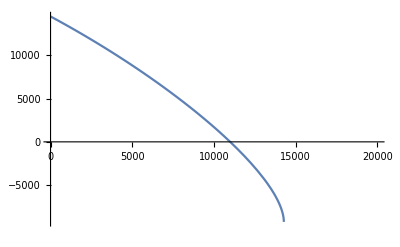

{po→10988.7}

5988.72

```mathematica
(*exemplo pagina 194 ISO 10400*)
ky=0.855;
pi=5000;
de=9.625;
t=0.545;
Ao=Pi 9.625^2/4
Ai=Pi (de-2t)^2/4
As=Ao-Ai
siga=20000;
sigy=80000;
feff=siga As -pi Ai+po Ao;
deltapmises=Sqrt[(ky(4./√3.)sigy t/(de-t))^2 (1.-(feff/(ky sigy As))^2)]-po+pi
MisesEq[pi,po,de,t,siga,sigy,ky]
Plot[{deltapmises,MisesEq[pi,po,de,t,siga,sigy,ky]},{po,0,20000}]
sol1=FindRoot[deltapmises,{po,10000}]
sol1[[1,2]]-pi
```

```mathematica
Hfunc[ov_,ec_,rs_,fy_]:=Max[0,0.127 ov+0.0039ec+0.440 rs/fy];
Hfunc[ov_,ec_,rs_]:=Max[0,0.127 ov+0.0039ec-0.440 rs];
ComputeColapseStrengthKTOld[vars_,ov_,ec_,rs_]:=Block[{siga,sigy,pi,d,t,young,nu,ke=0.825,sol,H,deltapec,deltapy,deltapmises,deltaptresca,ky=0.855,eq,po,Fa,Feff,Fy,Ai,Ao,As,kdr,BurstStrength, ColapseStrength,pyc,pec,pym,xi,Si,dt,c,val},
{siga,sigy,pi,d,t,young,nu}=vars;
deltaptresca=ky 2 sigy t/(d-t);
deltapmises= Sqrt[(ky(4./√3.)sigy t/(d-t))^2 (1.-(siga/(ky sigy))^2)];
(*Print["deltapmises = ",deltapmises];*)
deltapy=Min[(deltapmises+deltaptresca)/2,deltapmises];
(*deltapy=(deltapmises+deltaptresca)/2;*)
deltapec=ke (2. young)/(1.-nu^2)1./((d/t)(d/t-1.)^2);
(*H=Hfunc[ov,ec,rs];*)
H=0.22;
ColapseStrength=pi+(2. deltapy deltapec)/(deltapy+deltapec+Sqrt[(deltapy-deltapec)^2 +4. H deltapy deltapec]);
ColapseStrength

]
```

```mathematica
di=5.795;
de=7;
t=(de-di)/2;
ov=0.217;
ex=3.924;
rs=-0.237;
sigy=125000;
area=Pi/4(de^2-di^2)
Lvec={0,100,1480,2960,4440,5920,7400,8880,9066,10360,11840,13320,13885,14800};
PI={0.00,0.05,0.77,1.54,2.31,3.08,3.84,4.61,4.71,5.38,6.15,6.92,7.21,7.74};
PE={0.09,90.91,1345.45,2690.91,4036.36,5381.81,6727.27,8072.72,8241.81,9418.17,10763.62,12109.07,12622.71,13454.44};
DeltaP=PE-PI;
DeltaP=Table[{DeltaP[[i]],-Lvec[[i]]},{i,1,Length[DeltaP]}];
FA={303906,300110,247670,191430,135190,78950,22710,-33530,-40598,-89770,-146010,-202250,-223720,-258490};
Length[PI]
Length[PE]
Length[Lvec]
Length[FA]

KTRandomVarsData={{"KTme","NORMAL",0.9991,0.067*0.9991},{"YieldStress","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Ovality","NORMAL",0.217,0.541*0.217},{"Excent","NORMAL",3.924,0.661*3.924},{"Resid. Stress","NORMAL",-0.237,0.332*0.237},{"Nax","NORMAL",1.,0.01},{"Pint","NORMAL",1.,0.01},{"Pext","NORMAL",1.,0.01}}
M=Transpose[KTRandomVarsData][[3]]
SDev=Transpose[KTRandomVarsData][[4]]
distr=Transpose[KTRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
ov=0.217;
ex=3.924;
rs=-0.237;
sigy=95000;
area=Pi/4(de^2-di^2);
vars=Table[{FA[[i]]/area,sigy,PI[[i]],PE[[i]],de,t,3 10^7,0.3},{i,1,Length[FA]}];
```

12.1092

14

14

14

«1 more identical outputs»

{{KTme,NORMAL,0.9991,0.0669397},{YieldStress,NORMAL,1.1,0.04642},{Thickness,NORMAL,1.0069,0.0260787},{Ovality,NORMAL,0.217,0.117397},{Excent,NORMAL,3.924,2.59376},{Resid. Stress,NORMAL,-0.237,0.078684},{Nax,NORMAL,1.,0.01},{Pint,NORMAL,1.,0.01},{Pext,NORMAL,1.,0.01}}

{0.9991,1.1,1.0069,0.217,3.924,-0.237,1.,1.,1.}

{0.0669397,0.04642,0.0260787,0.117397,2.59376,0.078684,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{0.9991,0.0669397,0.9991,0.0669397,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{0.217,0.117397,0.217,0.117397,1},{3.924,2.59376,3.924,2.59376,1},{-0.237,0.078684,-0.237,0.078684,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

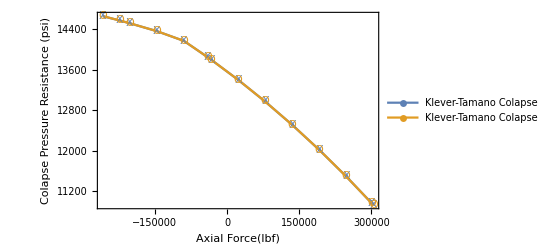

```mathematica
graphtamano=Table[{FA[[i]],ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[PI]}];
graphtamanoold=Table[{FA[[i]],ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]},{i,1,Length[PI]}];
ListLinePlot[{graphtamano,graphtamanoold},Frame->True,FrameLabel->{{"Colapse Pressure Resistance (psi)",""},{"Axial Force(lbf)",""}},PlotLegends->{"Klever-Tamano Colapse Resistance Iterative","Klever-Tamano Colapse Resistance No-Iterative"},PlotMarkers->{"X","O"}]
```

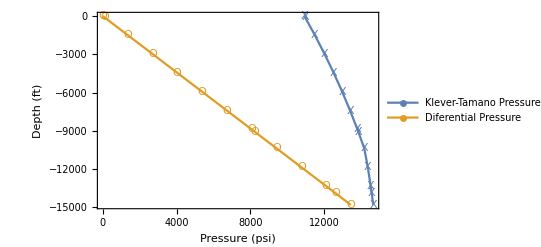

```mathematica
graphtamano=Table[{ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs],-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{graphtamano,DeltaP},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure (psi)",""}},PlotLegends->{"Klever-Tamano Pressure Resistance","Diferential Pressure"},PlotMarkers->{"X","O"}]
```

```mathematica
Table[checkconv[vars[[i]],M,ComputeNumericalGradKT],{i,1,3}]
```

tan = {12345.5,13120.4,14382.5,-560.877,-17.224,1943.29,-3014.76,0.,-0.09}

incval = {0.00118933,0.00169145,0.000985152,0.000167291,0.0147349,-0.000422794,0.001899,0.00270332,0.00445137}

estimateresidual = 44.1496

1.92261

1.95434

1.96744

1.97469

1.97932

1.98255

1.98493

1.98676

tan = {12383.1,13102.9,14439.2,-564.645,-17.3397,1956.34,-2965.19,0.0939729,-90.91}

incval = {0.00224783,0.00141389,0.00198652,0.000100468,0.00121497,-0.00101066,0.0030278,0.00147924,0.000233044}

estimateresidual = 63.9909

1.94327

1.96688

1.97649

1.98179

1.98517

1.98752

1.98925

1.99059

tan = {12888.2,12876.3,15211.3,-616.577,-18.9345,2136.28,-2314.15,1.45219,-1345.45}

incval = {0.00416609,0.000115428,0.00306215,0.0000517924,0.0180265,-0.000929847,0.0016995,9.68192×10^-6,0.00430565}

estimateresidual = 89.6733

1.96454

1.97943

1.98539

1.98863

1.99067

1.99208

1.9931

1.99388

{{0.000582709,0.0022091,0.00487931,0.00859345,0.0133517,0.019154,0.0260007,0.0338919,0.0428275,0},{0.00108955,0.00419014,0.00930205,0.0164255,0.0255608,0.0367081,0.0498678,0.0650401,0.0822252,0},{0.00160718,0.00627263,0.0139962,0.0247778,0.0386172,0.0555142,0.0754688,0.0984807,0.12455,0}}

| iter = 8  | residual = 1.00289×10^-7 | G(x) = 7.30523×10^-10| Beta = 14.9253

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| iter = 8  | residual = 1.12821×10^-7 | G(x) = 2.49609×10^-9| Beta = 14.8154

| iter = 7  | residual = 8.43947×10^-6 | G(x) = -0.000146033| Beta = 13.3047

| iter = 8  | residual = 8.16629×10^-6 | G(x) = -0.00024646| Beta = 11.7213

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

| iter = 8  | residual = 8.67517×10^-6 | G(x) = -0.000349454| Beta = 10.2129

| iter = 7  | residual = 0.0000441798 | G(x) = -0.00180298| Beta = 8.80426

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

| iter = 7  | residual = 9.47767×10^-6 | G(x) = -0.000318155| Beta = 7.50118

| iter = 6  | residual = 0.0000472725 | G(x) = -0.00127987| Beta = 6.29712

| iter = 6  | residual = 0.0000388607 | G(x) = -0.00101277| Beta = 6.15227

| iter = 6  | residual = 9.09728×10^-6 | G(x) = -0.000172102| Beta = 5.18099

| iter = 5  | residual = 0.0000878895 | G(x) = -0.00121346| Beta = 4.0487

| iter = 5  | residual = 0.0000123493 | G(x) = -0.0000884631| Beta = 2.97613

| iter = 5  | residual = 5.03012×10^-6 | G(x) = -0.0000239331| Beta = 2.58324

| iter = 4  | residual = 0.0000465839 | G(x) = -0.0010483| Beta = 1.96512

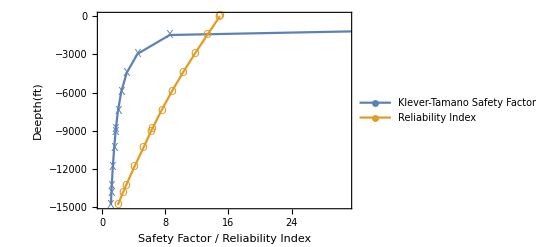

```mathematica
plotbeta=Table[{HRLF[RVVec,RX,ComputeNumericalGradKT,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
SF=Table[{ComputeColapseStrengthKT[{FA[[i]]/area,sigy,PI[[i]],de,t,3 10^7,0.3},ov,ex,rs]/(PE[[i]]-PI[[i]]),-Lvec[[i]]},{i,1,Length[Lvec]}];
ListLinePlot[{SF,plotbeta},Frame->True,FrameLabel->{{"Deepth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Klever-Tamano Safety Factor","Reliability Index"},PlotMarkers->{"X","O"}]
```

```mathematica
TableForm[PrependTo[SF,{"Safety Factor","Depth"}]]
TableForm[PrependTo[plotbeta,{"Reliability Index","Depth"}]]
```

Safety Factor | Depth
121417. | 0
120.699 | -100
8.545 | -1480
4.46866 | -2960
3.10153 | -4440
2.41193 | -5920
1.99347 | -7400
1.7107 | -8880
1.68143 | -9066
1.50551 | -10360
1.33526 | -11840
1.19977 | -13320
1.15537 | -13885
1.09033 | -14800

Reliability Index | Depth
14.9253 | 0
14.8154 | -100
13.3047 | -1480
11.7213 | -2960
10.2129 | -4440
8.80426 | -5920
7.50118 | -7400
6.29712 | -8880
6.15227 | -9066
5.18099 | -10360
4.0487 | -11840
2.97613 | -13320
2.58324 | -13885
1.96512 | -14800

```mathematica
KSRandomVarsData={{"meKS","NORMAL",1.004,0.047*1.004},{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069},{"Nax","NORMAL",1.0,0.01},{"Pext","NORMAL",1.0,0.01},{"Pint","NORMAL",1.0,0.01}};
```

```mathematica
M=Transpose[KSRandomVarsData][[3]]
SDev=Transpose[KSRandomVarsData][[4]]
distr=Transpose[KSRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
di=12.275;
de=13.375;
t=(de-di)/2;
sigy=80000;
area=Pi/4(de^2-di^2)
Lvec={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PI={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PE={0.05,311.69,623.38,935.06,1038.91,1039.01,1246.75,1558.43,1870.11,2181.79,2493.48,2805.16,3116.79,3116.89,3117.10,3233.72,3350.56,3467.39,3584.23,3701.06,3817.90,3934.74,4051.57,4168.41,4285.24,4328.52,4371.79,4415.06,4458.33,4501.61,4544.88,4588.15,4631.43,4674.70,4717.93};
FA={813678,767485,721285,675085,659693,659678,628885,582685,536485,490286,444086,397886,351686,670316,670345,685848,701386,716928,732477,748022,763568,779113,794656,810199,826082,832147,838213,844330,850524,856719,862914,869106,875297,881487,887678};
WELLCATSF={73.861,26.386,16.061,11.544,10.555,10.554,9.010,7.388,6.261,5.432,4.797,4.295,3.888,3.888,3.888,3.674,3.482,3.308,3.152,3.009,2.879,2.759,2.650,2.548,2.454,2.421,2.389,2.357,2.327,2.297,2.268,2.240,2.212,2.185,2.159};
Length[Lvec]
Length[PI]
Length[PE]
Length[FA]
(*n,de,t,fu,sa,pi,po*)
vars=Table[{0.104,de,t, sigy,FA[[i]]/area,PI[[i]],PE[[i]]},{i,1,Length[FA]}];
(*n,de,t,fu,sa,pi,po*)
```

{1.004,1.1,1.0069,1.,1.,1.}

{0.047188,0.04642,0.0260787,0.01,0.01,0.01}

{NORMAL,NORMAL,NORMAL,NORMAL,NORMAL,NORMAL}

{{1.004,0.047188,1.004,0.047188,1},{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1},{1.,0.01,1.,0.01,1}}

22.16

35

35

35

«1 more identical outputs»

```mathematica
vars[[3]]
```

{0.104,13.375,0.55,80000,32548.9,1200,623.38}

```mathematica
ComputeNumericalGradKS[vars[[3]],M]
```

{7280.78,{7826.09,7050.97,7492.51,-525.118,1249.25,-1200.}}

```mathematica
Table[checkconv[vars[[i]],M,ComputeNumericalGradKS],{i,1,2}]
```

tan = {7113.81,7731.15,7399.97,-1363.6,0.1002,0.}

incval = {0.00311164,0.00204644,0.0031245,0.00139954,0.00472992,0.00451039}

estimateresidual = 59.1702

1.93737

1.9634

1.97408

1.98

1.98379

1.98645

1.98842

1.98995

tan = {7479.68,7087.54,7456.39,-600.293,624.627,-600.}

incval = {0.00412866,0.0052855,0.00153158,0.00177871,0.00296667,0.000378462}

estimateresidual = 80.3205

1.95551

1.97427

1.98189

1.9861

1.9888

1.9907

1.99211

1.99322

{{0.00177919,0.00681443,0.0151066,0.0266568,0.0414657,0.0595344,0.0808638,0.105455,0.133308,0},{0.00272357,0.0105634,0.0235211,0.0415979,0.0647954,0.0931151,0.126558,0.165127,0.208821,0}}

```mathematica
ListLinePlot[{Table[{PE[[i]],-Lvec[[i]]},{i,1,Length[PE]}],Table[{PI[[i]],-Lvec[[i]]},{i,1,Length[PI]}]},Frame->True,FrameLabel->{{"Depth (ft)",""},{"Pressure(psi)",""}},PlotLegends->{"External Pressure","Internal Pressure"},PlotMarkers->{"X","O"}]
ListLinePlot[Table[{FA[[i]],-Lvec[[i]]},{i,1,Length[FA]}],Frame->True,FrameLabel->{{"Depth (ft)",""},{"Force(lbf)",""}},PlotLegends->{"Axial Force"},PlotMarkers->{"X"}]
graphst=Table[{FA[[i]],ComputeBurstResistance[0.104,de,t,sigy 1.15,FA[[i]]/area,PE[[i]]]},{i,1,Length[FA]}];
ListLinePlot[{graphst},Frame->True,FrameLabel->{{"Rupture Pressure Resistance (psi)",""},{"Axial Force(lbf)",""}},PlotLegends->{"Klever-Stewart Rupture Resistance"},PlotMarkers->{"X"}]
graphst=Table[{ComputeBurstResistance[0.104,de,t,sigy 1.15,FA[[i]]/area,PE[[i]]],-Lvec[[i]]},{i,1,Length[FA]}];
ListLinePlot[{graphst},Frame->True,FrameLabel->{{"Depth(ft)",""},{"Pressure(psi)",""}},PlotLegends->{"Klever-Stewart Pressure Resistance"},PlotMarkers->{"X"}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
MonteCarlo[RVVec,RX,ComputeNumericalGradKS,vars[[30]],1000]
```

Counter = 0

Pf Crude Monte Carlo  = 0.

β Crude Monte Carlo = ∞

```mathematica
sigy=80000;
plotbetaKS=Table[{HRLF[RVVec,RX,ComputeNumericalGradKS,vars[[i]]][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
SFKS=Table[{ComputeBurstResistance[0.104,de,t,sigy ,FA[[i]]/area,PE[[i]]]/(PI[[i]]-PE[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
SFWC=Table[{WELLCATSF[[i]],-Lvec[[i]]},{i,2,Length[Lvec]}];
ListLinePlot[{SFKS,plotbetaKS,SFWC},Frame->True,FrameLabel->{{"Deepth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Klever-Stewart Safety Factor","Reliability Index","WellCat Safety Factor"},PlotMarkers->{"X","O"}]
```

Min::nord: Invalid comparison with 991.628+885.56 ⅈ attempted.

Min::nord: Invalid comparison with 0.+1771.12 ⅈ attempted.

Min::nord: Invalid comparison with 991.628+885.56 ⅈ attempted.

General::stop: Further output of Min::nord will be suppressed during this calculation.

| iter = 13  | residual = 0.0000212988 | G(x) = 1.68774×10^-6| Beta = 21.2767

| iter = 60  | residual = 6.07188 | G(x) = -178.956| Beta = 20.418

| iter = 60  | residual = 0.711008 | G(x) = -346.233| Beta = 20.6377

| iter = 11  | residual = 0.0000416061 | G(x) = -0.000526059| Beta = 18.8779

| iter = 10  | residual = 0.0000841603 | G(x) = -0.00121185| Beta = 18.6362

| iter = 10  | residual = 0.0000839176 | G(x) = -0.00120803| Beta = 18.6365

| iter = 10  | residual = 0.0000150721 | G(x) = -0.000255229| Beta = 18.1698

| iter = 9  | residual = 0.0000537026 | G(x) = -0.00109606| Beta = 17.5118

| iter = 9  | residual = 0.0000110744 | G(x) = -0.000240337| Beta = 16.9025

| iter = 8  | residual = 0.0000546037 | G(x) = -0.00124815| Beta = 16.3389

| iter = 8  | residual = 0.0000282765 | G(x) = -0.000641685| Beta = 15.8172

| iter = 8  | residual = 0.0000143818 | G(x) = -0.000317537| Beta = 15.3331

| iter = 8  | residual = 7.30889×10^-6 | G(x) = -0.000155258| Beta = 14.8826

| iter = 9  | residual = 0.0000153352 | G(x) = -0.000514105| Beta = 14.7428

| iter = 9  | residual = 0.000015332 | G(x) = -0.000514066| Beta = 14.741

| iter = 9  | residual = 0.0000137644 | G(x) = -0.000464887| Beta = 14.4516

| iter = 8  | residual = 0.0000993186 | G(x) = -0.00388586| Beta = 14.1665

| iter = 8  | residual = 0.0000849096 | G(x) = -0.00336572| Beta = 13.887

| iter = 8  | residual = 0.0000717069 | G(x) = -0.00286321| Beta = 13.6133

| iter = 8  | residual = 0.0000598929 | G(x) = -0.00239473| Beta = 13.345

| iter = 8  | residual = 0.0000495288 | G(x) = -0.00197042| Beta = 13.0821

| iter = 8  | residual = 0.0000405794 | G(x) = -0.00159487| Beta = 12.8244

| iter = 8  | residual = 0.0000463491 | G(x) = -0.00184734| Beta = 12.5717

| iter = 8  | residual = 0.0000384807 | G(x) = -0.00150474| Beta = 12.3239

| iter = 8  | residual = 0.0000319107 | G(x) = -0.0012159| Beta = 12.08

| iter = 8  | residual = 0.0000297973 | G(x) = -0.00112269| Beta = 11.9904

| iter = 8  | residual = 0.0000278056 | G(x) = -0.00103448| Beta = 11.9014

| iter = 8  | residual = 0.0000259445 | G(x) = -0.000951856| Beta = 11.8129

| iter = 8  | residual = 0.0000242124 | G(x) = -0.00087481| Beta = 11.7248

| iter = 8  | residual = 0.0000225812 | G(x) = -0.00080202| Beta = 11.6373

| iter = 8  | residual = 0.0000210453 | G(x) = -0.000733283| Beta = 11.5502

| iter = 8  | residual = 0.0000195995 | G(x) = -0.000668424| Beta = 11.4638

| iter = 8  | residual = 0.0000182402 | G(x) = -0.000607326| Beta = 11.3779

| iter = 8  | residual = 0.0000169623 | G(x) = -0.000549801| Beta = 11.2925

| iter = 8  | residual = 0.0000157608 | G(x) = -0.000495671| Beta = 11.2075

-Graphics-

```mathematica
BarlowRandomVarsData={{"APIyield","NORMAL",1.1,0.0422*1.1},{"Thickness","NORMAL",1.0069,0.0259*1.0069}};
M=Transpose[BarlowRandomVarsData][[3]]
SDev=Transpose[BarlowRandomVarsData][[4]]
distr=Transpose[BarlowRandomVarsData][[2]]
nvars=Length[M];
RX=IdentityMatrix[nvars];
RVVec=Table[ComputeRandomVarData[distr[[i]],M[[i]],SDev[[i]]],{i,1,nvars}]
di=12.275;
de=13.375;
t=(de-di)/2;
sigy=80000;
area=Pi/4(de^2-di^2)
Lvec={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PI={0,600,1200,1800,2000,2000,2400,3000,3600,4200,4800,5400,6000,6000,6001,6270,6540,6810,7080,7350,7620,7890,8160,8430,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700};
PE={0.05,311.69,623.38,935.06,1038.91,1039.01,1246.75,1558.43,1870.11,2181.79,2493.48,2805.16,3116.79,3116.89,3117.10,3233.72,3350.56,3467.39,3584.23,3701.06,3817.90,3934.74,4051.57,4168.41,4285.24,4328.52,4371.79,4415.06,4458.33,4501.61,4544.88,4588.15,4631.43,4674.70,4717.93};
FA={813678,767485,721285,675085,659693,659678,628885,582685,536485,490286,444086,397886,351686,670316,670345,685848,701386,716928,732477,748022,763568,779113,794656,810199,826082,832147,838213,844330,850524,856719,862914,869106,875297,881487,887678};
WELLCATSF={73.861,26.386,16.061,11.544,10.555,10.554,9.010,7.388,6.261,5.432,4.797,4.295,3.888,3.888,3.888,3.674,3.482,3.308,3.152,3.009,2.879,2.759,2.650,2.548,2.454,2.421,2.389,2.357,2.327,2.297,2.268,2.240,2.212,2.185,2.159};
Length[Lvec]
Length[PI]
Length[PE]
Length[FA]
(*n,de,t,fu,sa,pi,po*)
vars={ sigy,t}
```

{1.1,1.0069}

{0.04642,0.0260787}

{NORMAL,NORMAL}

{{1.1,0.04642,1.1,0.04642,1},{1.0069,0.0260787,1.0069,0.0260787,1}}

22.16

35

35

35

«1 more identical outputs»

{80000,0.55}

```mathematica
ComputeBurstBarlow[vars_,Xvec_]:=Block[{d,sigy,t,strength,PI,PE,xvecn,derivative,i,xvecn1,dgdx,dx=0.0001},
{d,sigy,t,PI,PE}=vars;
Gx[xvec_]:= 0.875(2 sigy xvec[[1]])/(d/(t xvec[[2]]))-(PI-PE);
xvecn=Xvec;
derivative=Table[0,{Length[xvecn]}];

For[i=1,i≤Length[xvecn],i++,
xvecn1=xvecn;
xvecn1[[i]]+=dx;
dgdx=(Gx[xvecn1]-Gx[xvecn])/dx;
derivative[[i]]=dgdx;
];
{Gx[xvecn],derivative}
]
```

```mathematica
ComputeBurstBarlow[{de,sigy,t,1.05PI[[35]],PE[[35]]},M]
```

{909.336,{5796.73,6332.71}}

```mathematica
checkconv[{de,sigy,t,1.04PI[[35]],PE[[35]]},M,ComputeBurstBarlow]
```

tan = {5796.73,6332.71}

incval = {0.00139795,0.00173217}

estimateresidual = 19.0729

2.

2.

2.

«5 more identical outputs»

{0.000139405,0.000557621,0.00125465,0.00223048,0.00348513,0.00501859,0.00683086,0.00892193,0.0112918,0}

```mathematica
MonteCarlo[RVVec,RX,ComputeBurstBarlow,{de,sigy,t,1.04PI[[35]],PE[[35]]},100000]
```

Counter = 53

Pf Crude Monte Carlo  = 0.00053

β Crude Monte Carlo = 3.2741

```mathematica
HRLF[RVVec,RX,ComputeBurstBarlow,{de,sigy,t,1.04PI[[35]],PE[[35]]}]
```

| iter = 5  | residual = 1.38597×10^-6 | G(x) = -1.68768×10^-6| Beta = 3.29202

{3.29202,0.00049736,{-2.86861,-1.61508}}

```mathematica
plotbetaBarlow=Table[{HRLF[RVVec,RX,ComputeBurstBarlow,{de,sigy,t,PI[[i]],PE[[i]]}][[1]],-Lvec[[i]]},{i,1,Length[Lvec]}];
SFBarlow=Table[{ComputeBurstBarlow[{de,sigy,t,PI[[i]],PE[[i]]},M][[1]]/(PI[[i]]-PE[[i]]),-Lvec[[i]]},{i,2,Length[Lvec]}];
```

| iter = 7  | residual = 0.0000179389 | G(x) = 4.00012×10^-7| Beta = 23.6969

| iter = 7  | residual = 4.15102×10^-6 | G(x) = -1.27331×10^-6| Beta = 22.6162

| iter = 6  | residual = 0.0000770421 | G(x) = -0.000262417| Beta = 21.5184

| iter = 7  | residual = 1.42546×10^-6 | G(x) = -3.37219×10^-6| Beta = 20.4046

| iter = 7  | residual = 2.12047×10^-6 | G(x) = -6.03296×10^-6| Beta = 20.0299

| iter = 7  | residual = 2.11955×10^-6 | G(x) = -6.02926×10^-6| Beta = 20.0303

| iter = 7  | residual = 4.78809×10^-6 | G(x) = -0.0000184998| Beta = 19.2768

| iter = 7  | residual = 0.0000121302 | G(x) = -0.0000660673| Beta = 18.1376

| iter = 7  | residual = 0.0000205353 | G(x) = -0.000142393| Beta = 16.9906

| iter = 7  | residual = 0.0000248676 | G(x) = -0.000202874| Beta = 15.8396

| iter = 7  | residual = 0.0000229062 | G(x) = -0.000205931| Beta = 14.689

| iter = 7  | residual = 0.00001676 | G(x) = -0.000156918| Beta = 13.5431

| iter = 7  | residual = 0.0000100354 | G(x) = -0.0000930802| Beta = 12.4058

| iter = 7  | residual = 0.0000100375 | G(x) = -0.0000931008| Beta = 12.4062

| iter = 7  | residual = 0.0000100208 | G(x) = -0.0000929381| Beta = 12.4031

| iter = 7  | residual = 7.09631×10^-6 | G(x) = -0.0000642871| Beta = 11.807

| iter = 7  | residual = 4.77778×10^-6 | G(x) = -0.0000417639| Beta = 11.2117

| iter = 6  | residual = 0.0000802259 | G(x) = -0.000667174| Beta = 10.6207

| iter = 6  | residual = 0.0000528473 | G(x) = -0.00041446| Beta = 10.0344

| iter = 6  | residual = 0.000033627 | G(x) = -0.00024591| Beta = 9.45298

| iter = 6  | residual = 0.0000206474 | G(x) = -0.000139211| Beta = 8.87674

| iter = 6  | residual = 0.000012212 | G(x) = -0.0000750419| Beta = 8.30581

| iter = 6  | residual = 6.93958×10^-6 | G(x) = -0.0000384036| Beta = 7.74027

| iter = 6  | residual = 3.77611×10^-6 | G(x) = -0.0000185835| Beta = 7.18027

| iter = 6  | residual = 1.95836×10^-6 | G(x) = -8.45497×10^-6| Beta = 6.62578

| iter = 5  | residual = 0.0000917621 | G(x) = -0.000374033| Beta = 6.42186

| iter = 5  | residual = 0.0000749028 | G(x) = -0.000289254| Beta = 6.21867

| iter = 5  | residual = 0.0000607813 | G(x) = -0.00022188| Beta = 6.01624

| iter = 5  | residual = 0.000049015 | G(x) = -0.000168743| Beta = 5.81458

| iter = 5  | residual = 0.0000392666 | G(x) = -0.000127176| Beta = 5.61371

| iter = 5  | residual = 0.0000312344 | G(x) = -0.000094923| Beta = 5.41356

| iter = 5  | residual = 0.0000246586 | G(x) = -0.0000701248| Beta = 5.21418

| iter = 5  | residual = 0.0000193116 | G(x) = -0.0000512421| Beta = 5.01558

| iter = 5  | residual = 0.0000149929 | G(x) = -0.000037004| Beta = 4.8177

| iter = 5  | residual = 0.0000115297 | G(x) = -0.0000263799| Beta = 4.62043

```mathematica
ListLinePlot[{SFKS,plotbetaKS,SFWC,SFBarlow,plotbetaBarlow},Frame->True,FrameLabel->{{"Deepth(ft)",""},{"Safety Factor / Reliability Index",""}},PlotLegends->{"Klever-Stewart Safety Factor","Reliability Index KS","WellCat Safety Factor","Barlow Safety Factor","Reliability Index Barlow"},PlotMarkers->{"X","O","H","K"}]
```

-Graphics-

```mathematica
SFBarlow
```

{{21.1165,-600},{10.0582,-1200},{6.37208,-1800},{5.63456,-2000},{5.63525,-2000},{4.52908,-2400},{3.42324,-3000},{2.68602,-3600},{2.15944,-4200},{1.76451,-4800},{1.45734,-5400},{1.21156,-6000},{1.21164,-6000},{1.21104,-6001},{1.10007,-6270},{0.999224,-6540},{0.907613,-6810},{0.824035,-7080},{0.747468,-7350},{0.677075,-7620},{0.612133,-7890},{0.55203,-8160},{0.49625,-8430},{0.444338,-8700},{0.426017,-8800},{0.408152,-8900},{0.390728,-9000},{0.373731,-9100},{0.357147,-9200},{0.340956,-9300},{0.325146,-9400},{0.309708,-9500},{0.294623,-9600},{0.279871,-9700}}